NDSolve::ndnum: Encountered non-numerical value for a derivative at x == 0..

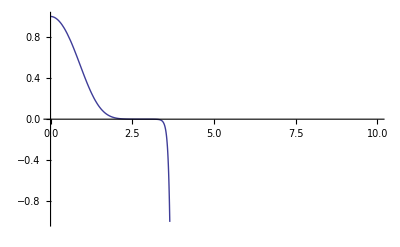

```mathematica
s=NDSolve[{1/2 D[psi[x],x,x]==(x^4-e)psi[x],psi[0]==1,psi'[0]==0},psi[x],{x,0,10}]/.e->0.667986302;
Plot[Evaluate[psi[x]/.s],{x,0,10},PlotRange->{-1,1}]
```

```mathematica
guess[a_,x_]:=x Exp[-a x^2];
```

```mathematica
Integrate[(-1/2 D[guess[a,x],x,x]+x^4 guess[a,x]) guess[a,x],{x,-Infinity,Infinity},Assumptions->Re[a]>0]/Integrate[guess[a,x]^2,{x,-Infinity,Infinity},Assumptions->Re[a]>0]
```

(3 (5+8 a^3))/(16 a^2)

```mathematica
Eg[x_]:=(3 (5+8 x^3))/(16 x^2)
```

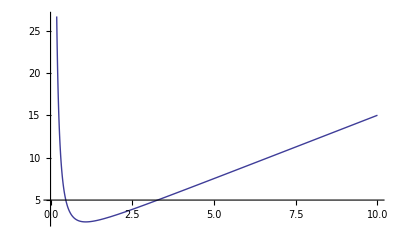

```mathematica
Plot[Eg[x],{x,0,10}]
```

```mathematica
N[9/8*10^(1/3)]
```

2.42374

NDSolve::ndnum: Encountered non-numerical value for a derivative at x == 0..

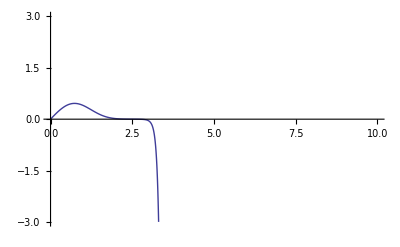

```mathematica
s=NDSolve[{1/2 D[psi[x],x,x]==(x^4-e)psi[x],psi[0]==0,psi'[0]==1},psi[x],{x,0,10}]/.e->2.39365;
Plot[Evaluate[psi[x]/.s],{x,0,10},PlotRange->{-3,3}]
```